## Zestaw 4 poprawa

Katarzyna Sowa

## 3N

Zbudowano wielomian interpolacyjny oparty na nastepujacych danych:

```mathematica
Subscript[x, 0]=-1.2300;
Subscript[y, 0]=1.5129;
Subscript[x, 1]=-1.1900;
Subscript[y, 1]=1.4161;
Subscript[x, 2]=-0.7400;
Subscript[y, 2]=0.5476;
Subscript[x, 3]=0.1100;
Subscript[y, 3]=0.0121;
Subscript[x, 4]=2.5600;
Subscript[y, 4]=6.5536;
```

```mathematica
p[t_]:=N[Subscript[y, 0]((t - Subscript[x, 1]) (t - Subscript[x, 2])(t - Subscript[x, 3])(t-Subscript[x, 4]))/((Subscript[x, 0]-Subscript[x, 1]) (Subscript[x, 0]-Subscript[x, 2]) (Subscript[x, 0]-Subscript[x, 3])(Subscript[x, 0]-Subscript[x, 4]))+Subscript[y, 1]((t - Subscript[x, 0]) (t - Subscript[x, 2])(t - Subscript[x, 3])(t-Subscript[x, 4]))/((Subscript[x, 1]-Subscript[x, 0])  (Subscript[x, 1]-Subscript[x, 2]) (Subscript[x, 1]-Subscript[x, 3])(Subscript[x, 1]-Subscript[x, 4]))+
            Subscript[y, 2]((t - Subscript[x, 0]) (t - Subscript[x, 1]) (t - Subscript[x, 3]))/((Subscript[x, 2]-Subscript[x, 0]) (Subscript[x, 2]-Subscript[x, 1])  (Subscript[x, 2]-Subscript[x, 3])(Subscript[x, 2]-Subscript[x, 4]))+Subscript[y, 3]((t - Subscript[x, 0]) (t - Subscript[x, 1]) (t - Subscript[x, 2])(t-Subscript[x, 4]))/((Subscript[x, 3]-Subscript[x, 0]) (Subscript[x, 3]-Subscript[x, 1])  (Subscript[x, 3]-Subscript[x, 2])(Subscript[x, 3]-Subscript[x, 4]))+Subscript[y, 4]((t - Subscript[x, 0]) (t - Subscript[x, 1]) (t - Subscript[x, 2])(t-Subscript[x, 3]))/((Subscript[x, 4]-Subscript[x, 0]) (Subscript[x, 4]-Subscript[x, 1])  (Subscript[x, 4]-Subscript[x, 2])(Subscript[x, 4]-Subscript[x, 3]))];
```

```mathematica
p[t]
```

15.1988 (-2.56+t) (-0.11+t) (0.74+t) (1.19+t)-16.1379 (-2.56+t) (-0.11+t) (0.74+t) (1.23+t)+0.885364 (-0.11+t) (1.19+t) (1.23+t)-0.00333543 (-2.56+t) (0.74+t) (1.19+t) (1.23+t)+0.0570334 (-0.11+t) (0.74+t) (1.19+t) (1.23+t)

```mathematica
Expand[p[t]]
```

-0.507477+3.91695 t+7.22066 t^2+1.10671 t^3-0.885364 t^4

## 5N

Skonstruowano funckje, jak w zadaniu 4N:

```mathematica
f[x_]:=1/(1+5 x^2);
```

```mathematica
X=Table[x,{x,-1,1,1/32}];
```

```mathematica
Y=Map[f,X];
```

```mathematica
XY=N[Transpose[Distribute[{X,Y}]]];
```

```mathematica
SplajnNat[XY0_] := Module[{XY=XY0}, 
Dd= Module[{k}, n = Length[XY]-1; X = Transpose[XY]_⟦1⟧; Y = Transpose[XY]_⟦2⟧; h=d = Table[0,{n}]; m = Table[0,{n+1}]; a=b=c=v = Table[0,{n-1}]; s = Table[0,{n},{4}]; 
h_⟦1⟧ = X_⟦2⟧ - X_⟦1⟧; 
d_⟦1⟧ = (Y_⟦2⟧ - Y_⟦1⟧)/h_⟦1⟧; 
For[ k=2, k≤n, k++, 
h_⟦k⟧ = X_⟦k+1⟧ - X_⟦k⟧; 
d_⟦k⟧ = (Y_⟦k+1⟧ - Y_⟦k⟧)/h_⟦k⟧; 
a_⟦k-1⟧ = h_⟦k⟧; 
b_⟦k-1⟧ = 2 (h_⟦k-1⟧ + h_⟦k⟧); 
c_⟦k-1⟧ = h_⟦k⟧; 
v_⟦k-1⟧ = 6 (d_⟦k⟧ - d_⟦k-1⟧)]; ]; 
TrD:=Module[{k,t}, 
m_⟦1⟧ = 0; 
m_⟦n+1⟧ = 0;
For[ k=2, k≤n-1, k++, 
t = a_⟦k-1⟧/b_⟦k-1⟧; 
b_⟦k⟧  =  b_⟦k⟧ - t  c_⟦k-1⟧; 
v_⟦k⟧  =  v_⟦k⟧ - t  v_⟦k-1⟧; ]; 
m_⟦n⟧  =  v_⟦n-1⟧/b_⟦n-1⟧; 
For[ k=n-2, 1≤k, k--, 
m_⟦k+1⟧ = (v_⟦k⟧ - c_⟦k⟧ m_⟦k+2⟧)/b_⟦k⟧; ]; ]; 
Pol:=Module[{k}, 
For[ k=1, k≤n, k++, 
s_⟦k,1⟧ = Y_⟦k⟧; 
s_⟦k,2⟧ = d_⟦k⟧ - 1/6 h_⟦k⟧ (2 m_⟦k⟧+m_⟦k+1⟧); 
s_⟦k,3⟧ = m_⟦k⟧/2; 
s_⟦k,4⟧ = (m_⟦k+1⟧ - m_⟦k⟧)/(6 h_⟦k⟧); ]; ]; 
CS[t_]:=Module[{j}, 
For[ j=1, j≤n, j++, 
If[ X_⟦j⟧≤t && t<X_⟦j+1⟧,k=j ]; ]; 
If[t<X_⟦1⟧,k=1 ]; 
If[X_⟦n+1⟧≤t,k=n ]; 
w = t - X_⟦k⟧; 
Return[ ((s_⟦k,4⟧ w+s_⟦k,3⟧) w+s_⟦k,2⟧) w+s_⟦k,1⟧ ]; ]; 

Dd; 
TrD; 
Pol; ]
```

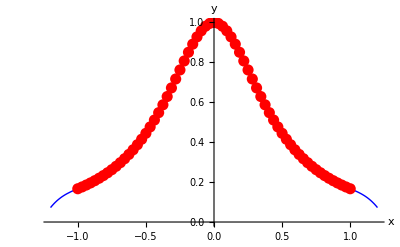

Splajn y = 5.15425-14.3955 x+14.1119 x^2-4.70397 x^3

```mathematica
SplajnNat[XY];   
dots=ListPlot[XY,PlotStyle->{Red,PointSize[0.02]},DisplayFunction->Identity];  
gr=Plot[CS[x],{x,-1.2,1.2},PlotStyle->{Blue},DisplayFunction->Identity];  
Show[gr,dots,AxesLabel->{"x","y    "}] 
Print["Splajn y = ",Expand[CS[x]]];
```